## 能带计算

将薛定谔方程，利用Bloch定理，对波函数进行展开，得到如下的等式：
-Graphics-
其中-Graphics-且-Graphics-我们令质量m和约化普朗克常数ℏ为1，进而有方程：
-Graphics-
其中注意矢量运算：-Graphics-
利用上述等式构造矩阵，便可求解其本征值，进而画出能带E(k)

为了验证程序思路的正确性，可以先从一维入手。将参量设为：

```mathematica
Clear["Global`*"];
Lk=5;(*倒空间大小,2Lk+1维的矩阵*)
a=1;(*晶格常数*)
b1=(2Pi)/a;(*单位倒格矢*)
```

构造矩阵：

```mathematica
(*动能项的构造*)
list1=Table[(n*b1+kx)^2/2,{n,-Lk,Lk}];
M=DiagonalMatrix[list1];
(*势场的傅里叶系数*)
V=DiracDelta[x/(2Pi)];
coff=Table[FourierCoefficient[1.V,x,i],{i,-2Lk,2Lk}];
center=(Length[coff]+1)/2;
Table[{M[[i,j]]=M[[i,j]]+coff[[center+j-i]]},{j,1,2Lk+1},{i,1,2Lk+1}];
```

为了讨论方便，以上将势能设为DiracComb的形式，下面绘制1D的能带图：

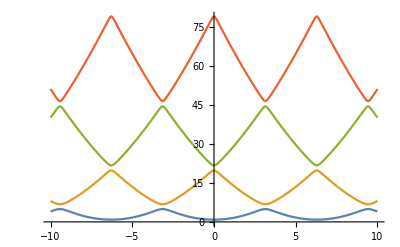

```mathematica
(*绘制能带*)
Table[Subscript[Ek, i]=Eigenvalues[M][[i]],{i,1,4}];
Plot[{Subscript[Ek, 1],Subscript[Ek, 2],Subscript[Ek, 3],Subscript[Ek, 4]},{kx,-10,10}]
```

下面将k空间扩展到二维，类似的参数和矩阵构造如下：

```mathematica
Clear["Global`*"];
Lk=1;(*倒空间大小,(2Lk+1)^2 维的矩阵*)
(*晶格常数*)
a1=1;
a2=1;
(*单位倒格矢*)
b1=(2Pi)/a1;
b2=(2Pi)/a2;
(*动能项的构造*)
list1=Table[(kx^2+ky^2+(n1*b1)^2+(n2*b2)^2+2*(n1*b1*kx+n2*b2*ky))/2,{n1,-Lk,Lk},{n2,-Lk,Lk}]//Flatten;
M=DiagonalMatrix[list1];
M0=M;
(*势场的傅里叶系数*)
V=DiracComb[x/(2Pi)]DiracComb[y/(2Pi)];
coff=Table[FourierCoefficient[1.V,{x,y},{i,j}],{i,-Lk,Lk},{j,-Lk,Lk}]//Flatten;
center=(Length[coff]+1)/2;
Table[{M[[i,j]]=M[[i,j]]+coff[[Mod[center+j-i,9,1]]]},{j,1,Length[list1]},{i,1,Length[list1]}];
```

首先画出不加周期性势场下的能带作为对比：

```mathematica
eig=Eigenvalues[M0];
Table[Subscript[Ek, i]=eig[[i]],{i,1,4}];
Plot3D[{Subscript[Ek, 1],Subscript[Ek, 2],Subscript[Ek, 3],Subscript[Ek, 4]},{kx,-2Pi,2Pi},{ky,-2Pi,2Pi}]
```

-Graphics3D-

其次，画出施加势场下产生的能带:

```mathematica
eig=Eigenvalues[M];
Table[Subscript[Ek, i]=eig[[i]],{i,1,4}];
Plot3D[{Subscript[Ek, 1],Subscript[Ek, 2],Subscript[Ek, 3],Subscript[Ek, 4]},{kx,-2Pi,2Pi},{ky,-2Pi,2Pi}]
```

-Graphics3D-

可以明显的看到出现了能隙，进而说明程序的正确性。也可画出密度图，可以大致看出等能面的形貌：

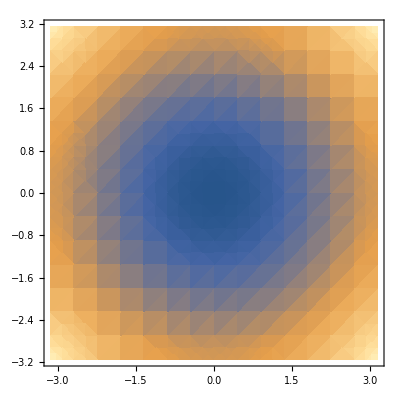
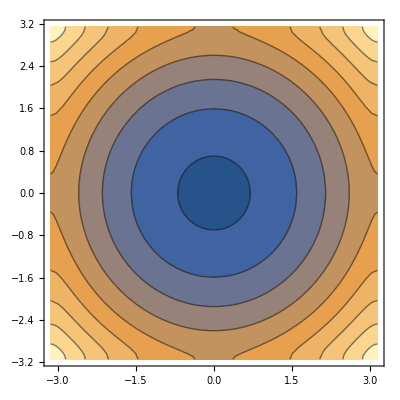

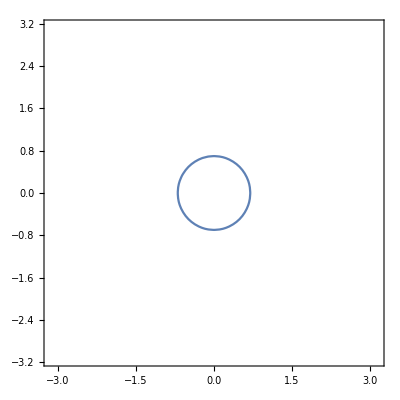
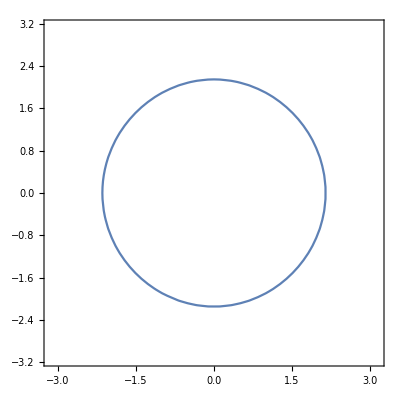
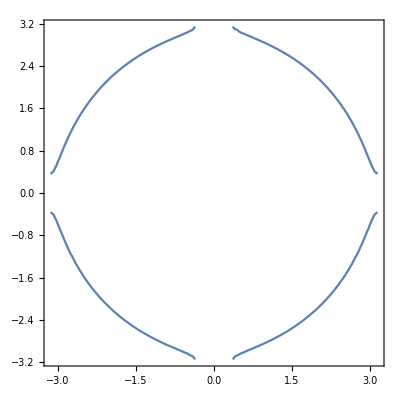
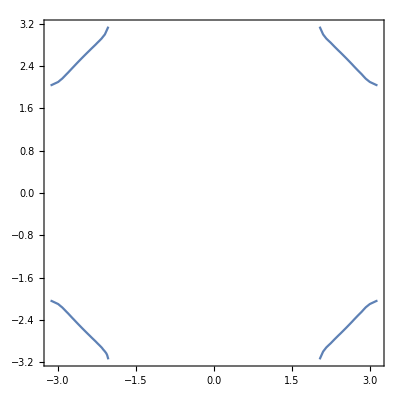

```mathematica
{DensityPlot[Subscript[Ek, 1],{kx,-Pi,Pi},{ky,-Pi,Pi}],ContourPlot[Subscript[Ek, 1],{kx,-Pi,Pi},{ky,-Pi,Pi}]}
Table[ContourPlot[Subscript[Ek, 1]==i,{kx,-Pi,Pi},{ky,-Pi,Pi}],{i,1,8,2}]
```

可以看到，在能量增大的过程中，当等能面碰到边界时，会出现裂开，这符合固体物理的理论。
下面对三维的能带进行尝试：

```mathematica
Clear["Global`*"];
Lk=1;(*倒空间大小,(2Lk+1)^2 维的矩阵*)
(*晶格常数*)
a1=1;
a2=1;
a3=1;
(*单位倒格矢*)
b1=(2.Pi)/a1;
b2=(2.Pi)/a2;
b3=(2.Pi)/a3;
(*动能项的构造*)
list1=Table[(kx^2+ky^2+kz^2+(n1*b1)^2+(n2*b2)^2+(n3*b3)^2+2*(n1*b1*kx+n2*b2*ky+n3*b3*kz))/2,{n1,-Lk,Lk},{n2,-Lk,Lk},{n3,-Lk,Lk}]//Flatten;
M=DiagonalMatrix[list1];
M0=M;
(*势场的傅里叶系数*)
M=M+Table[1,Length[list1],Length[list1]];
```

由于三维需要在四维空间下才能完全表达能带，因此这里仅画出等能面。首先画出不加势场的等能面：

```mathematica
eig=Eigenvalues[M0];
Table[Subscript[Ek, i]=eig[[i]],{i,1,4}];
ContourPlot3D[{Subscript[Ek, 1]==1},{kx,-Pi,Pi},{ky,-Pi,Pi},{kz,-Pi,Pi}]
```

-Graphics3D-

由于计算时间复杂度过大，因此利用紧束缚的方法进行等能面的绘制：

```mathematica
ContourPlot3D[{Cos[0.5kx]Cos[0.5ky]+Cos[0.5kz]Cos[0.5ky]+Cos[0.5kx]Cos[0.5kz]==0.8},{kx,-Pi,Pi},{ky,-Pi,Pi},{kz,-Pi,Pi}]
```

-Graphics3D-